## 0 зад. Решете моделната задача u' (x) = -10 u, 0 < x ≤ 1 u (0) = 1 при n = 4, 20, 100 и сравнете с точното решение.

```mathematica
explicitEuler[n_,f_]:= (
h=1.0/n;(*compute numerically*)
xList=Table[i*h,{i,0,n}];
yList=Table[0,{n+1}];

yList[[1]] = 1;
For[i=1, i<n+1, i++,
yList[[i+1]] = yList[[i]]+h*f[xList[[i]],yList[[i]]]
];

Transpose[{xList,yList}]
)
```

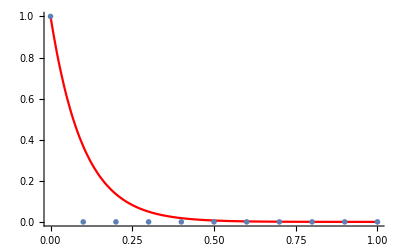

```mathematica
(*Compute the exact solution*)
f[x_,u_]:=-10*u
exact[t_]=DSolve[{u'[t]==f[t,u[t]],u[0]==1},u[t],t][[1,1,2]];
(*exact[x_]:=E^(-10x);*)
plotExact = Plot[exact[x],{x,0, 1}, PlotStyle->Red, PlotRange->All];

n=10(*4,100*);
appr = explicitEuler[n,f];
plotAppr = ListPlot[appr, PlotMarkers->●];
Show[plotExact, plotAppr]
```

```mathematica
implicitEuler[n_,f_]:= (
h=1.0/n;
xList=Table[i*h,{i,0,n}];
yList=Table[0,{n+1}];

yList[[1]] =1;
For[i=1, i<n+1, i++,
initialGuess =yList[[i]]+h*f[xList[[i]],yList[[i]]];
yList[[i+1]]=FindRoot[yNew==  yList[[i]]+h*f[xList[[i+1]],yNew],{yNew,initialGuess}][[1,2]]
];

Transpose[{xList,yList}]
)
```

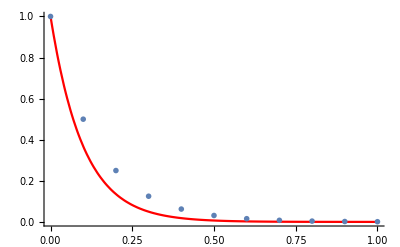

```mathematica
n=10(*4,20*);
appr = implicitEuler[n,f];
plotAppr = ListPlot[appr, PlotMarkers->●];
Show[plotExact, plotAppr]
```

## 1 зад. Пресметнете локалната грешка на апроксимация за явния и неявния метод на Ойлер.

## 2зад. Като използвате явния и неявния метод на Ойлер, решете моделното уравнение du/dx=-10u, 0<x≤1 u(0)=1 при n=100, 1000,10000. Начертайте графиките на абсолютните грешки по модул и ги сравнете.

## 3 зад. Пресметнете локалната грешка на апроксимация на диференчните схеми (а) (y_(i+1)-y_i)/h=1/(3h)(y_i-y_(i-1))+2/3 f_i (b)y_(i+1)=y_i+h/2(3 f_i-f_(i-1))

## 4 зад. Да се реши задачата на Коши du/dt=10u(1-u), 0<t≤6 u(0)=0.1 с явния и неявния метод на Ойлер за n=10,20, 35, 75, 500. Да се изобразят резултатите.

## 5 зад. Да се изобразят точните решения на задачата на Коши du/dt=u(u-2), 0<t≤6 u(0)=а при a=-0.5,0, 1, 2, 2.5.

## 6 зад. Намерете равновесните точки на ОДУ du/dt=u^3(5-u)(u-3) Определете кои от тях са устойчиви.

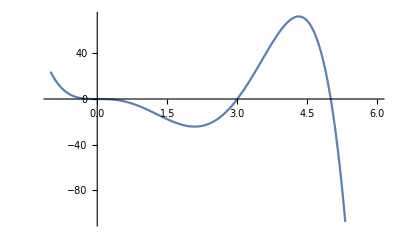

```mathematica
Plot[u^3(5-u)(u-3),{u,-1,6}]
```

```mathematica
(*Ustoichivite sa 0 i 5 *)
```

## 7 зад. Нека да приложим явния и неявния метод върху задачата du/dt=10u(1-u), 0<t≤6. u(0)=0.1 Определете при какви стойности на стъпката h методите са А-устойчиви и монотонни.

```mathematica
f[u_] := 10u(1-u)
f'[1] (* toest lambda = -10. Togava h < 5.*)
```

-10

```mathematica
appr = explicitEuler[25,f,0,6,0.1];
```

```mathematica
Show[Plot[exact[x],{x,0,6},PlotStyle -> Red, PlotRange->All],ListLinePlot[appr,PlotRange->All]]
```

ListLinePlot::lpn: explicitEuler[25.,f,0.,6.,0.1] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListLinePlot[explicitEuler[25,f,0,6,0.1],PlotRange→All]].

Show[-Graphics-,ListLinePlot[explicitEuler[25,f,0,6,0.1],PlotRange→All]]

## 8зад. Определете при какви стойности на стъпката h явния и неявния метод на Ойлер са А-устойчиви и монотонни за задачата du/dt=20 sin(u), 0<t≤0.5 u(0)=π/2.

## 9 зад. Имплементирайте подобрения метод на Ойлер.